```mathematica
(*a={50,100,1};
b={650,966,1};
c={45,10,1};
d={434,53,1};
e={1650,1400,1};
f={210,1200,1};
g={300,922,1};
h={1172,1470,1};
i={1050,533,1};
j={1747,1010,1};
k={51,35,1};
l={135,350,1};
m={780,115,1};
n={110,1080,1};
o={1649,308,1};
p={188,875,1};
q={1580,275,1};
r={149,180,1};*)

a={300,300,-415,1};
b={1500,1100,-415,1};
c={500,515,-415,1};
d={315,500,-1415,1};
e={312,333,-615,1};
f={155,301,-615,1};
g={1620,1120,-1615,1};
h={358,589,-1615,1};
i={800,800,-615,1};
j={1252,1152,-1315,1};
k={152,252,-315,1};
l={725,666,-1715,1};
m={418,811,-915,1};
n={611,128,-1815,1};
o={1100,1100,-815,1};
p={127,245,-1315,1};
q={1255,223,-515,1};
r={656,324,-715,1};



(*K1={{2663.969662, 0, 945.6292097,0},{0, 2664.587487, 707.7870042,0},{0, 0, 1,0}};
K2={{4337.370912, 0, 966.352207,0},{0,4332.858039,752.2296946,0},{0,0,1,0}};*)

K1={{17.3158028, 0, 6.146589863,0},{0 ,17.31981867, 4.600615527,0},{0, 0, 1,0}};

K2={{18.60732121, 0, 4.145650968,0},{0, 18.58796099, 3.22706539,0},{0, 0, 1,0}};

PC1={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r};

RotationsE3[alpha_]:=Module[{Re3},
Re3 = {{Cos[alpha Degree],-Sin[alpha Degree ],0},{Sin[alpha Degree ], Cos[alpha Degree],0},{0,0,1}};
Return[Re3]
];

ComputeTranslationAndRotation[PC1_,K1_,K2_]:=Module[{V1,V2,M1,R1,R2,M2,PM1,PM2},
R1=RotationsE3[0];
R2=RotationsE3[45];

PxPC1={};
PxPC2={};

(*PxPC1=Map[(#/6.5)*1000&,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r}];
PxPC2=Map[(#/4.29)*#*1000&,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r}];

Print["PxPC1 = ",MatrixForm[PxPC1]];
Print["PxPC2 = ",MatrixForm[PxPC2]];*)

t={-1600,-70,550};(*im mm*)

(*Compile t in mm in t in px*)

(*t=(t/4.29)*1000;*)

Print["t = ", t];
V1={{1,0,0,0},{0,1,0,0},{0,0,1,0}};
V2= {{1,0,0,-t[[1]]},{0,1,0,-t[[2]]},{0,0,1,-t[[3]]}};

Print["V1 = ", MatrixForm[V1]];
Print["V2 = ", MatrixForm[V2]];

R1=Transpose[R1];
R2=Transpose[R2];

Print["R1 = ", N[R1]];
Print["R2 = ", N[R2]];
(*V1= {{1,0,0,0},{0,1,0,0},{0,0,1,0}};
V2= {{1,0,0,0},{0,1,0,0},{0,0,1,0}};*)

M1 =R1.V1;
M2=R2.V2;

Print["M1 = ",MatrixForm[M1]];
Print["M2 = ", MatrixForm[N[M2]]];

M1={{M1[[1,1]],M1[[1,2]],M1[[1,3]],M1[[1,4]]},{M1[[2,1]],M1[[2,2]],M1[[2,3]],M1[[2,4]]},{M1[[3,1]],M1[[3,2]],M1[[3,3]],M1[[3,4]]},{0,0,0,1}};
M2={{M2[[1,1]],M2[[1,2]],M2[[1,3]],M2[[1,4]]},{M2[[2,1]],M2[[2,2]],M2[[2,3]],M2[[2,4]]},{M2[[3,1]],M2[[3,2]],M2[[3,3]],M2[[3,4]]},{0,0,0,1}};

Print["M1 = ", MatrixForm[M1]];
Print["M2 = ", MatrixForm[N[M2]]];

Print["K1 = ", MatrixForm[K1]];
Print["K2 = ", MatrixForm[K2]];

PM1=K1.M1;
PM2=K2.M2;

Print["PM1 = ", MatrixForm[PM1]];
Print["PM2 = ", MatrixForm[PM2]];

(*projectedPointsK1 = Map[PM1.#&,PC1];
projectedPointsK2 = Map[PM2.#&,PC1];*)

projectedPointsK1 = Map[PM1.#&,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r}];
projectedPointsK2 = Map[PM2.#&,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r}];
Print["projectedPointsK1 = ", MatrixForm[projectedPointsK1]];
Print["projectedPointsK2 = ", MatrixForm[projectedPointsK2]];

For[ee=1,ee≤ Length[projectedPointsK1],ee++,
projectedPointsK1 [[ee]]= (projectedPointsK1[[ee]]/6.5)*1000;
projectedPointsK2[[ee]] = (projectedPointsK2[[ee]]/4.29)*1000;
];

Print["projectedPointsK1 in px= ", MatrixForm[projectedPointsK1]];
Print["projectedPointsK2 in px= ", MatrixForm[projectedPointsK2]];

For[ii = 1, ii≤ Length[projectedPointsK1], ii++,
projectedPointsK1[[ii]]=projectedPointsK1[[ii]]/projectedPointsK1[[ii,3]];
projectedPointsK2[[ii]]=projectedPointsK2[[ii]]/projectedPointsK2[[ii,3]];
];

Print["projectedPointsK1 in px= ", MatrixForm[projectedPointsK1]];
Print["projectedPointsK2 in px= ", MatrixForm[projectedPointsK2]];
NormalizeCoordinates[projectedPointsK1,projectedPointsK2];

];
```

t = {-1600,-70,550}

V1 = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

V2 = (1 | 0 | 0 | 1600
0 | 1 | 0 | 70
0 | 0 | 1 | -550)

R1 = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R2 = {{0.707107,0.707107,0.},{-0.707107,0.707107,0.},{0.,0.,1.}}

M1 = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

M2 = (0.707107 | 0.707107 | 0. | 1180.87
-0.707107 | 0.707107 | 0. | -1081.87
0. | 0. | 1. | -550.)

M1 = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

M2 = (0.707107 | 0.707107 | 0. | 1180.87
-0.707107 | 0.707107 | 0. | -1081.87
0. | 0. | 1. | -550.
0. | 0. | 0. | 1.)

K1 = (17.3158 | 0 | 6.14659 | 0
0 | 17.3198 | 4.60062 | 0
0 | 0 | 1 | 0)

K2 = (18.6073 | 0 | 4.14565 | 0
0 | 18.588 | 3.22707 | 0
0 | 0 | 1 | 0)

PM1 = (17.3158 | 0. | 6.14659 | 0.
0. | 17.3198 | 4.60062 | 0.
0. | 0. | 1. | 0.)

PM2 = (13.1574 | 13.1574 | 4.14565 | 19692.7
-13.1437 | 13.1437 | 3.22707 | -21884.7
0. | 0. | 1. | -550.)

projectedPointsK1 = (2643.91 | 3286.69 | -415.
23422.9 | 17142.5 | -415.
6107.07 | 7010.45 | -415.
-3242.95 | 2150.04 | -1415.
1622.38 | 2938.12 | -615.
-1096.2 | 2383.89 | -615.
18124.9 | 11968.2 | -1615.
-3727.69 | 2771.38 | -1615.
10072.5 | 11026.5 | -615.
13596.6 | 13902.6 | -1315.
695.826 | 2915.4 | -315.
2012.56 | 3644.94 | -1715.
1613.88 | 9836.81 | -915.
-576.105 | -6133.18 | -1815.
14037.9 | 15302.3 | -815.
-5883.66 | -1806.45 | -1315.
18565.8 | 1493. | -515.
6964.35 | 2322.18 | -715.)

projectedPointsK2 = (25866.7 | -23223.9 | -965.
52181.4 | -28481.4 | -965.
31327. | -23026.8 | -965.
24549.8 | -24019.4 | -1965.
25629.6 | -23593.3 | -1165.
23142.9 | -21950.4 | -1165.
49048.6 | -33668.3 | -2165.
25457.5 | -24060.2 | -2165.
38194.9 | -23869.4 | -1165.
45871.5 | -27442.7 | -1865.
23702.4 | -21586.9 | -865.
30884.8 | -28194.6 | -2265.
32069.8 | -19672. | -1465.
21891.6 | -34090.2 | -2365.
45260.2 | -24514.8 | -1365.
19135.7 | -24577.3 | -1865.
37004.3 | -37110.9 | -1065.
29622.8 | -28555.8 | -1265.)

projectedPointsK1 in px= (406755. | 505645. | -63846.2
3.60352×10^6 | 2.63731×10^6 | -63846.2
939549. | 1.07853×10^6 | -63846.2
-498915. | 330775. | -217692.
249597. | 452019. | -94615.4
-168647. | 366752. | -94615.4
2.78844×10^6 | 1.84126×10^6 | -248462.
-573490. | 426366. | -248462.
1.54961×10^6 | 1.69638×10^6 | -94615.4
2.09179×10^6 | 2.13886×10^6 | -202308.
107050. | 448523. | -48461.5
309624. | 560761. | -263846.
248289. | 1.51336×10^6 | -140769.
-88631.6 | -943566. | -279231.
2.15968×10^6 | 2.3542×10^6 | -125385.
-905178. | -277916. | -202308.
2.85628×10^6 | 229693. | -79230.8
1.07144×10^6 | 357259. | -110000.)

projectedPointsK2 in px= (6.02952×10^6 | -5.41351×10^6 | -224942.
1.21635×10^7 | -6.63902×10^6 | -224942.
7.30232×10^6 | -5.36755×10^6 | -224942.
5.72257×10^6 | -5.59893×10^6 | -458042.
5.97427×10^6 | -5.49961×10^6 | -271562.
5.39461×10^6 | -5.11664×10^6 | -271562.
1.14332×10^7 | -7.84808×10^6 | -504662.
5.93415×10^6 | -5.60844×10^6 | -504662.
8.90324×10^6 | -5.56395×10^6 | -271562.
1.06926×10^7 | -6.39689×10^6 | -434732.
5.52503×10^6 | -5.0319×10^6 | -201632.
7.19925×10^6 | -6.57217×10^6 | -527972.
7.47548×10^6 | -4.58555×10^6 | -341492.
5.10294×10^6 | -7.94644×10^6 | -551282.
1.05502×10^7 | -5.7144×10^6 | -318182.
4.46054×10^6 | -5.72898×10^6 | -434732.
8.6257×10^6 | -8.65056×10^6 | -248252.
6.90507×10^6 | -6.65635×10^6 | -294872.)

projectedPointsK1 in px= (-6.37086 | -7.91974 | 1.
-56.4406 | -41.3073 | 1.
-14.7158 | -16.8927 | 1.
2.29184 | -1.51946 | 1.
-2.63801 | -4.77743 | 1.
1.78244 | -3.87624 | 1.
-11.2228 | -7.41065 | 1.
2.30816 | -1.71602 | 1.
-16.378 | -17.9292 | 1.
-10.3396 | -10.5723 | 1.
-2.20897 | -9.25524 | 1.
-1.1735 | -2.12533 | 1.
-1.7638 | -10.7506 | 1.
0.317413 | 3.37916 | 1.
-17.2244 | -18.7758 | 1.
4.47427 | 1.37373 | 1.
-36.0502 | -2.89903 | 1.
-9.74036 | -3.24781 | 1.)

projectedPointsK2 in px= (-26.8048 | 24.0663 | 1.
-54.074 | 29.5144 | 1.
-32.4632 | 23.862 | 1.
-12.4936 | 12.2236 | 1.
-21.9997 | 20.2518 | 1.
-19.8651 | 18.8415 | 1.
-22.6553 | 15.5512 | 1.
-11.7587 | 11.1133 | 1.
-32.7853 | 20.4887 | 1.
-24.596 | 14.7146 | 1.
-27.4016 | 24.9559 | 1.
-13.6357 | 12.4479 | 1.
-21.8907 | 13.428 | 1.
-9.2565 | 14.4145 | 1.
-33.1576 | 17.9595 | 1.
-10.2604 | 13.1782 | 1.
-34.7458 | 34.8459 | 1.
-23.4172 | 22.5737 | 1.)

CemtroidPC1 = {-9.72739,-8.679,1.}

CemtroidPC2 = {-24.0701,19.1351,1.}

Mean[IntermediatePC1] = {1.57898×10^-15,4.93432×10^-17}

Mean[IntermediatePC2] = {-1.38161×10^-15,3.15797×10^-15}

MeanDistPC1 = 13.246

MeanDistPC2 = 10.3524

(0.106765 | 0. | 1.03854
0. | 0.106765 | 0.926614
0. | 0. | 1.)

Matrix normalization PC1= {{0.35836,0.0810633},{-4.98734,-3.48357},{-0.532591,-0.876931},{1.28323,0.764389},{0.756897,0.416551},{1.22885,0.512767},{-0.15966,0.135416},{1.28498,0.743403},{-0.710057,-0.987601},{-0.0653668,-0.202142},{0.802704,-0.0615219},{0.913256,0.699703},{0.850233,-0.221175},{1.07243,1.28739},{-0.800423,-1.07799},{1.51624,1.07328},{-2.81035,0.617099},{-0.00138483,0.579862}}

1.41421

(0.136607 | 0. | 3.28814
0. | 0.136607 | -2.61399
0. | 0. | 1.)

Matrix normalization PC2 = {{-0.37359,0.673638},{-4.09875,1.4179},{-1.14656,0.645728},{1.58143,-0.944151},{0.28283,0.152554},{0.574424,-0.0400984},{0.193271,-0.489586},{1.68183,-1.09583},{-1.19057,0.18492},{-0.0718418,-0.603871},{-0.455113,0.795171},{1.42541,-0.913507},{0.297721,-0.779626},{2.02364,-0.644866},{-1.24143,-0.160584},{1.8865,-0.813749},{-1.45838,2.14622},{0.0891842,0.469747}}

1.41421

Begin Computation of Fundamentalmatrix________________________________________________

CoefficientMtx = (-0.13388 | -0.0302844 | -0.37359 | 0.241405 | 0.0546073 | 0.673638 | 0.35836 | 0.0810633 | 1.
20.4419 | 14.2783 | -4.09875 | -7.07153 | -4.93933 | 1.4179 | -4.98734 | -3.48357 | 1.
0.610648 | 1.00545 | -1.14656 | -0.343909 | -0.566259 | 0.645728 | -0.532591 | -0.876931 | 1.
2.02935 | 1.20883 | 1.58143 | -1.21157 | -0.721699 | -0.944151 | 1.28323 | 0.764389 | 1.
0.214073 | 0.117813 | 0.28283 | 0.115468 | 0.0635466 | 0.152554 | 0.756897 | 0.416551 | 1.
0.70588 | 0.294546 | 0.574424 | -0.0492748 | -0.0205611 | -0.0400984 | 1.22885 | 0.512767 | 1.
-0.0308578 | 0.026172 | 0.193271 | 0.0781675 | -0.0662976 | -0.489586 | -0.15966 | 0.135416 | 1.
2.16111 | 1.25027 | 1.68183 | -1.40812 | -0.814646 | -1.09583 | 1.28498 | 0.743403 | 1.
0.84537 | 1.17581 | -1.19057 | -0.131303 | -0.182627 | 0.18492 | -0.710057 | -0.987601 | 1.
0.00469607 | 0.0145222 | -0.0718418 | 0.0394731 | 0.122068 | -0.603871 | -0.0653668 | -0.202142 | 1.
-0.365321 | 0.0279994 | -0.455113 | 0.638287 | -0.0489204 | 0.795171 | 0.802704 | -0.0615219 | 1.
1.30177 | 0.997366 | 1.42541 | -0.834266 | -0.639184 | -0.913507 | 0.913256 | 0.699703 | 1.
0.253132 | -0.0658486 | 0.297721 | -0.662864 | 0.172434 | -0.779626 | 0.850233 | -0.221175 | 1.
2.17022 | 2.60521 | 2.02364 | -0.691576 | -0.830194 | -0.644866 | 1.07243 | 1.28739 | 1.
0.993669 | 1.33825 | -1.24143 | 0.128535 | 0.173108 | -0.160584 | -0.800423 | -1.07799 | 1.
2.86038 | 2.02474 | 1.8865 | -1.23384 | -0.873381 | -0.813749 | 1.51624 | 1.07328 | 1.
4.09857 | -0.899966 | -1.45838 | -6.03164 | 1.32443 | 2.14622 | -2.81035 | 0.617099 | 1.
-0.000123505 | 0.0517146 | 0.0891842 | -0.000650518 | 0.272388 | 0.469747 | -0.00138483 | 0.579862 | 1.)

Rank CoefficientMatx = 8

FFin = (-0.134144 | 0.134113 | -0.652675
-0.134283 | -0.134252 | -0.335861
0.163862 | 0.593806 | -0.0985912)

FFin Rank = 2

PC2NormTest = {{-0.37359,0.673638,1.},{-4.09875,1.4179,1.},{-1.14656,0.645728,1.},{1.58143,-0.944151,1.},{0.28283,0.152554,1.},{0.574424,-0.0400984,1.},{0.193271,-0.489586,1.},{1.68183,-1.09583,1.},{-1.19057,0.18492,1.},{-0.0718418,-0.603871,1.},{-0.455113,0.795171,1.},{1.42541,-0.913507,1.},{0.297721,-0.779626,1.},{2.02364,-0.644866,1.},{-1.24143,-0.160584,1.},{1.8865,-0.813749,1.},{-1.45838,2.14622,1.},{0.0891842,0.469747,1.}}

PC1NormTest = {{0.35836,0.0810633,1.},{-4.98734,-3.48357,1.},{-0.532591,-0.876931,1.},{1.28323,0.764389,1.},{0.756897,0.416551,1.},{1.22885,0.512767,1.},{-0.15966,0.135416,1.},{1.28498,0.743403,1.},{-0.710057,-0.987601,1.},{-0.0653668,-0.202142,1.},{0.802704,-0.0615219,1.},{0.913256,0.699703,1.},{0.850233,-0.221175,1.},{1.07243,1.28739,1.},{-0.800423,-1.07799,1.},{1.51624,1.07328,1.},{-2.81035,0.617099,1.},{-0.00138483,0.579862,1.}}

l = {{{-0.512217,-0.376132,0.240202},{0.0873039,0.0241774,0.071733},{-0.412271,-0.268588,0.096968},{-0.991437,-0.421467,-0.400097},{-0.670156,-0.394321,0.0383414},{-0.735108,-0.407613,-0.0282756},{-0.744261,-0.296086,-0.357641},{-1.02525,-0.414584,-0.473716},{-0.468168,-0.200814,-0.183874},{-0.724025,-0.245143,-0.468945},{-0.484982,-0.381501,0.29901},{-0.966398,-0.40463,-0.407466},{-0.79717,-0.271174,-0.512752},{-1.01062,-0.521027,-0.149919},{-0.507682,-0.147599,-0.397371},{-1.01487,-0.479938,-0.272675},{-0.169208,-0.428159,0.936872},{-0.60164,-0.410902,0.194961}}}

lPrime = {{{0.104905,0.630983,-0.35971},{1.30067,0.392617,4.32652},{0.353063,0.640108,0.543545},{-0.11092,0.663282,-1.19285},{0.00639322,0.639392,-0.732503},{-0.0698361,0.689769,-1.07285},{0.167095,0.554213,-0.0398657},{-0.108336,0.666334,-1.18694},{0.39173,0.631166,0.696542},{0.199775,0.612177,0.0119636},{0.0644458,0.709718,-0.601833},{-0.0526038,0.622348,-0.929654},{0.0795089,0.737526,-0.579233},{-0.152873,0.564797,-1.23093},{0.415989,0.631181,0.785879},{-0.183656,0.653062,-1.44868},{0.457987,0.134055,1.5284},{0.086182,0.515772,-0.292441}}}

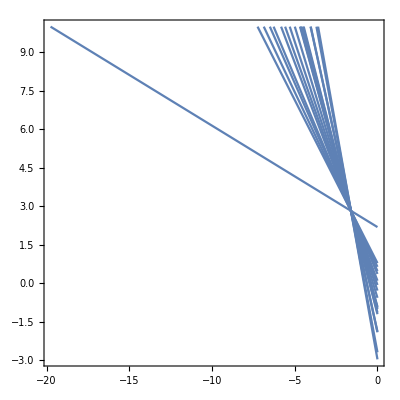

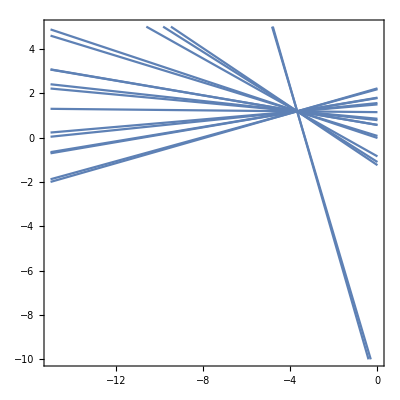

FPrime MatrixRank = 2

FPrime = (-0.134144 | 0.134113 | -0.652675
-0.134283 | -0.134252 | -0.335861
0.163862 | 0.593806 | -0.0985912)

2

lRank2 = {{{-0.512217,-0.376132,0.240202},{0.0873039,0.0241774,0.071733},{-0.412271,-0.268588,0.096968},{-0.991437,-0.421467,-0.400097},{-0.670156,-0.394321,0.0383414},{-0.735108,-0.407613,-0.0282756},{-0.744261,-0.296086,-0.357641},{-1.02525,-0.414584,-0.473716},{-0.468168,-0.200814,-0.183874},{-0.724025,-0.245143,-0.468945},{-0.484982,-0.381501,0.29901},{-0.966398,-0.40463,-0.407466},{-0.79717,-0.271174,-0.512752},{-1.01062,-0.521027,-0.149919},{-0.507682,-0.147599,-0.397371},{-1.01487,-0.479938,-0.272675},{-0.169208,-0.428159,0.936872},{-0.60164,-0.410902,0.194961}}}

lPrime = {{{0.104905,0.630983,-0.35971},{1.30067,0.392617,4.32652},{0.353063,0.640108,0.543545},{-0.11092,0.663282,-1.19285},{0.00639322,0.639392,-0.732503},{-0.0698361,0.689769,-1.07285},{0.167095,0.554213,-0.0398657},{-0.108336,0.666334,-1.18694},{0.39173,0.631166,0.696542},{0.199775,0.612177,0.0119636},{0.0644458,0.709718,-0.601833},{-0.0526038,0.622348,-0.929654},{0.0795089,0.737526,-0.579233},{-0.152873,0.564797,-1.23093},{0.415989,0.631181,0.785879},{-0.183656,0.653062,-1.44868},{0.457987,0.134055,1.5284},{0.086182,0.515772,-0.292441}}}

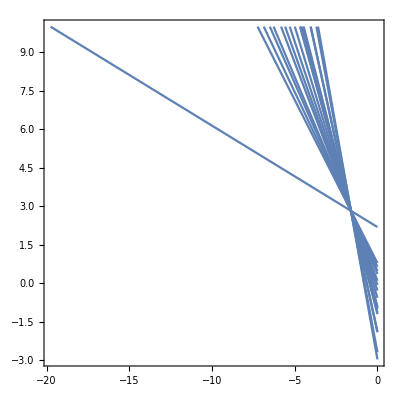

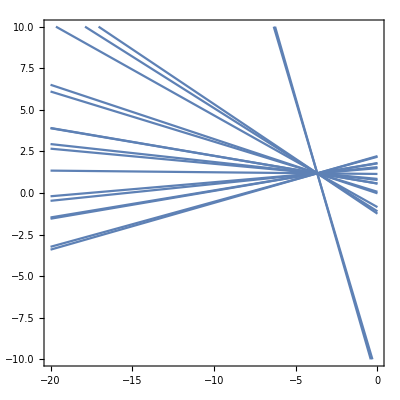

Demnormalized FPrime -> F =(-0.00195647 | 0.00195601 | -0.0912152
-0.00195851 | -0.00195805 | -0.0819261
0.00787856 | 0.147947 | -0.00607807)

F Rank = 2

8.88178×10^-16

-4.44089×10^-16

4.44089×10^-16

-2.77556×10^-16

7.21645×10^-16

-2.77556×10^-16

-2.22045×10^-16

-3.33067×10^-16

1.33227×10^-15

2.22045×10^-16

2.77556×10^-16

-3.88578×10^-16

-2.22045×10^-16

-9.99201×10^-16

0.

-7.77156×10^-16

1.66533×10^-16

-2.22045×10^-16

lRank2De = {{{0.00830156,-0.0765517,3.34326},{0.0723095,-0.0338127,3.93445},{0.0189723,-0.0650698,3.26845},{-0.0428624,-0.0813919,1.70393},{-0.00856075,-0.0784937,2.81678},{-0.0154954,-0.0799129,2.62495},{-0.0164726,-0.0680057,2.11617},{-0.0464721,-0.0806571,1.54545},{0.0130045,-0.0578339,2.76685},{-0.0143121,-0.0625667,1.97711},{0.0112093,-0.0771249,3.47018},{-0.0401891,-0.0795943,1.72812},{-0.0221215,-0.0653459,1.80808},{-0.0449102,-0.0920215,2.05356},{0.00878579,-0.0521524,2.38974},{-0.0453642,-0.0876346,1.86275},{0.044923,-0.0821065,4.87551},{-0.00124565,-0.0802639,3.14913}}}

lPrimeRank2De = {{{0.0358538,0.150992,1.22387},{0.199204,0.11843,8.52632},{0.069754,0.152239,2.72018},{0.00637053,0.155405,-0.0906446},{0.0223964,0.152141,0.625945},{0.0119829,0.159023,0.148901},{0.0443495,0.140505,1.62474},{0.00672356,0.155821,-0.0760305},{0.0750362,0.151017,2.95672},{0.0488137,0.148423,1.8032},{0.0303268,0.161748,0.95366},{0.014337,0.149813,0.275083},{0.0323845,0.165547,1.03556},{0.000639442,0.141951,-0.311873},{0.0783502,0.151019,3.10328},{-0.00356565,0.154008,-0.526743},{0.0840874,0.0831083,3.51975},{0.0332961,0.135254,1.14847}}}

-Graphics-

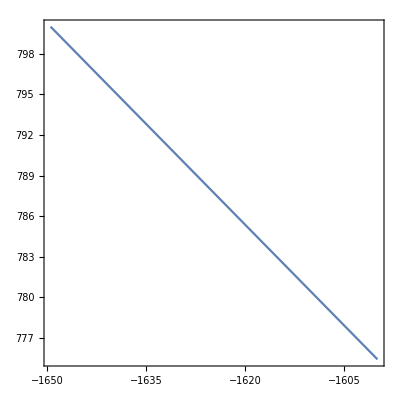

epipole ={-0.998281,0.0540886,0.0225719}

epipolePrime = {0.668781,-0.743224,-0.0186785}

Test F^T.e' = {0,0,0}

Test F.e = {0,0,0}

End Computation of Fundamentalmatrix________________________________________________

Begin Computation of Essential Matrix with K1 and K2___________________________________

PC1mm = (-6.37086 | -7.91974 | 1.
-56.4406 | -41.3073 | 1.
-14.7158 | -16.8927 | 1.
2.29184 | -1.51946 | 1.
-2.63801 | -4.77743 | 1.
1.78244 | -3.87624 | 1.
-11.2228 | -7.41065 | 1.
2.30816 | -1.71602 | 1.
-16.378 | -17.9292 | 1.
-10.3396 | -10.5723 | 1.
-2.20897 | -9.25524 | 1.
-1.1735 | -2.12533 | 1.
-1.7638 | -10.7506 | 1.
0.317413 | 3.37916 | 1.
-17.2244 | -18.7758 | 1.
4.47427 | 1.37373 | 1.
-36.0502 | -2.89903 | 1.
-9.74036 | -3.24781 | 1.)

PC2mm = (-26.8048 | 24.0663 | 1.
-54.074 | 29.5144 | 1.
-32.4632 | 23.862 | 1.
-12.4936 | 12.2236 | 1.
-21.9997 | 20.2518 | 1.
-19.8651 | 18.8415 | 1.
-22.6553 | 15.5512 | 1.
-11.7587 | 11.1133 | 1.
-32.7853 | 20.4887 | 1.
-24.596 | 14.7146 | 1.
-27.4016 | 24.9559 | 1.
-13.6357 | 12.4479 | 1.
-21.8907 | 13.428 | 1.
-9.2565 | 14.4145 | 1.
-33.1576 | 17.9595 | 1.
-10.2604 | 13.1782 | 1.
-34.7458 | 34.8459 | 1.
-23.4172 | 22.5737 | 1.)

PC1 in mm = (-6.37086 | -7.91974 | 1.
-56.4406 | -41.3073 | 1.
-14.7158 | -16.8927 | 1.
2.29184 | -1.51946 | 1.
-2.63801 | -4.77743 | 1.
1.78244 | -3.87624 | 1.
-11.2228 | -7.41065 | 1.
2.30816 | -1.71602 | 1.
-16.378 | -17.9292 | 1.
-10.3396 | -10.5723 | 1.
-2.20897 | -9.25524 | 1.
-1.1735 | -2.12533 | 1.
-1.7638 | -10.7506 | 1.
0.317413 | 3.37916 | 1.
-17.2244 | -18.7758 | 1.
4.47427 | 1.37373 | 1.
-36.0502 | -2.89903 | 1.
-9.74036 | -3.24781 | 1.)

PC2 in mm = (-26.8048 | 24.0663 | 1.
-54.074 | 29.5144 | 1.
-32.4632 | 23.862 | 1.
-12.4936 | 12.2236 | 1.
-21.9997 | 20.2518 | 1.
-19.8651 | 18.8415 | 1.
-22.6553 | 15.5512 | 1.
-11.7587 | 11.1133 | 1.
-32.7853 | 20.4887 | 1.
-24.596 | 14.7146 | 1.
-27.4016 | 24.9559 | 1.
-13.6357 | 12.4479 | 1.
-21.8907 | 13.428 | 1.
-9.2565 | 14.4145 | 1.
-33.1576 | 17.9595 | 1.
-10.2604 | 13.1782 | 1.
-34.7458 | 34.8459 | 1.
-23.4172 | 22.5737 | 1.)

normalized Coordinates K1 = (-0.722892 | -0.722892 | 1.
-3.61446 | -2.6506 | 1.
-1.20482 | -1.24096 | 1.
-0.222615 | -0.353357 | 1.
-0.507317 | -0.541463 | 1.
-0.252033 | -0.489431 | 1.
-1.0031 | -0.693498 | 1.
-0.221672 | -0.364706 | 1.
-1.30081 | -1.30081 | 1.
-0.952091 | -0.876046 | 1.
-0.48254 | -0.8 | 1.
-0.422741 | -0.388338 | 1.
-0.456831 | -0.886339 | 1.
-0.336639 | -0.0705234 | 1.
-1.34969 | -1.34969 | 1.
-0.0965779 | -0.186312 | 1.
-2.43689 | -0.43301 | 1.
-0.917483 | -0.453147 | 1.)

normalized Coordinates K2 = (-1.66335 | 1.12111 | 1.
-3.12886 | 1.41421 | 1.
-1.96744 | 1.11012 | 1.
-0.894229 | 0.483999 | 1.
-1.40511 | 0.915901 | 1.
-1.29039 | 0.840031 | 1.
-1.44034 | 0.663015 | 1.
-0.854734 | 0.424264 | 1.
-1.98475 | 0.928647 | 1.
-1.54464 | 0.618008 | 1.
-1.69542 | 1.16897 | 1.
-0.955609 | 0.496067 | 1.
-1.39925 | 0.548792 | 1.
-0.720262 | 0.601863 | 1.
-2.00476 | 0.792581 | 1.
-0.774216 | 0.535354 | 1.
-2.09011 | 1.70104 | 1.
-1.48129 | 1.04082 | 1.)

EsMtx = {{-0.630376,0.630376,-1.75359},{-0.630376,-0.630376,-1.91405},{-0.113462,2.59341,-1.11022×10^-15}}

2

SVD of EMtx ={{{0.716721,-1.24366×10^-15,-0.69736},{0.621641,0.453178,0.638899},{0.316028,-0.89142,0.324802}},{{2.74471,0.,0.},{0.,2.74471,0.},{0.,0.,0.}},{{-0.320445,-0.0672313,-0.944878},{0.320445,-0.946365,-0.0413384},{-0.89142,-0.316028,0.324802}}}

new SVD = {{{0.716721,-1.24366×10^-15,-0.69736},{0.621641,0.453178,0.638899},{0.316028,-0.89142,0.324802}},{{2.74471,0.,0.},{0.,2.74471,0.},{0.,0.,0.}},{{-0.320445,-0.0672313,-0.944878},{0.320445,-0.946365,-0.0413384},{-0.89142,-0.316028,0.324802}}}

EPrime = {{-0.630376,0.630376,-1.75359},{-0.630376,-0.630376,-1.91405},{-0.113462,2.59341,-5.21805×10^-15}}

2

-1.22125×10^-15

-6.21725×10^-15

-2.22045×10^-15

-4.21885×10^-15

-1.9984×10^-15

-2.88658×10^-15

-3.33067×10^-15

-4.10783×10^-15

-1.9984×10^-15

-3.10862×10^-15

-1.9984×10^-15

-3.66374×10^-15

-4.66294×10^-15

-4.13558×10^-15

-3.55271×10^-15

-3.94129×10^-15

-2.22045×10^-16

-1.88738×10^-15

End Computation of Essential Matrix with K1 and K2___________________________________

Begin Reconstruction of Rotation and Translation________________________________________________

E = (-0.630376 | 0.630376 | -1.75359
-0.630376 | -0.630376 | -1.91405
-0.113462 | 2.59341 | -1.11022×10^-15)

U of E = {{0.716721,-1.24366×10^-15,-0.69736},{0.621641,0.453178,0.638899},{0.316028,-0.89142,0.324802}}

Sigma of E = {{2.74471,0.,0.},{0.,2.74471,0.},{0.,0.,0.}}

V of E = {{-0.320445,-0.0672313,-0.944878},{0.320445,-0.946365,-0.0413384},{-0.89142,-0.316028,0.324802}}

S1 = (0. | -0.324802 | 0.638899
0.324802 | 0. | 0.69736
-0.638899 | -0.69736 | 0.)

S2 = (0. | 0.324802 | -0.638899
-0.324802 | 0. | -0.69736
0.638899 | 0.69736 | 0.)

R1 = (0.707107 | 0.707107 | -1.05471×10^-15
-0.707107 | 0.707107 | -1.80411×10^-15
-3.33067×10^-16 | 1.81626×10^-15 | 1.)

R2 = (0.610735 | -0.649451 | -0.453008
-0.500257 | -0.759929 | 0.415031
-0.613796 | -0.0268536 | -0.789007)

Check if t of S1, S2 is equal = {{{-0.69736,0.638899,0.324802}},{{0.69736,-0.638899,-0.324802}}}

R1 is Rotation = {{1.,0,0},{0,1.,0},{0,0,1.}}

R2 is Rotation ={{1.,0,0},{0,1.,0},{0,0,1.}}

Determinant of R1 = 1.

Determinant of R2 = 1.

Left E und S = {{-0.944878,-0.0413384,0.324802}} , {{0.69736,-0.638899,-0.324802}}

P1 = (0.707107 | 0.707107 | -1.05471×10^-15 | -0.944878
-0.707107 | 0.707107 | -1.80411×10^-15 | -0.0413384
-3.33067×10^-16 | 1.81626×10^-15 | 1. | 0.324802)

P2 = (0.707107 | 0.707107 | -1.05471×10^-15 | 0.944878
-0.707107 | 0.707107 | -1.80411×10^-15 | 0.0413384
-3.33067×10^-16 | 1.81626×10^-15 | 1. | -0.324802)

P3 = (0.610735 | -0.649451 | -0.453008 | -0.944878
-0.500257 | -0.759929 | 0.415031 | -0.0413384
-0.613796 | -0.0268536 | -0.789007 | 0.324802)

P4 = (0.610735 | -0.649451 | -0.453008 | 0.944878
-0.500257 | -0.759929 | 0.415031 | 0.0413384
-0.613796 | -0.0268536 | -0.789007 | -0.324802)

{2.39992,2.47999,-0.0437221}

(0.187858 | 0.247936 | -0.102187
-0.381595 | -0.236316 | -0.892654
0.497929 | 0.691193 | -0.410881)

End Reconstruction of Rotation and Translation________________________________________________

```mathematica
ComputeTranslationAndRotation[PC1,K1,K2];
```